-2.33811

-4.08795

-5.52056

-6.78671

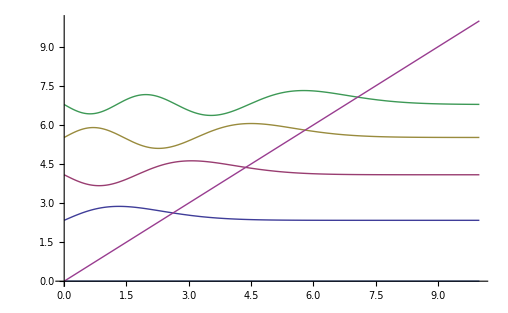

```mathematica
x1 = x/.FindRoot[AiryAi[x],{x,-2}]
x2 = x/.FindRoot[AiryAi[x],{x,-4}]
x3 = x/.FindRoot[AiryAi[x],{x,-6}]
x4 = x/.FindRoot[AiryAi[x],{x,-7}]
Plot[{AiryAi[x+x1]-x1,AiryAi[x+x2]-x2,AiryAi[x+x3]-x3,AiryAi[x+x4]-x4, 0, x},{x, 0, 10}]
```